### Start choosing the example:

```mathematica
t=24;
```

```mathematica
alpha
beta
A
Parameters
```

2

1

1

<|alpha→2,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$23991[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$23991[x$]-g$23991[m$]]|>

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced1"][[2]]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,1},{3,2}},Exit Vertices and Terminal Costs→{{4,1}},Switching Costs→{}|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.611622,Null}

<|j59→1,j60→2,u88→1,j55→1,j56→3,j57→2,j58→3,j61→0,j62→0,j63→0,j64→0,j65→0,j66→0,jt67→0,jt68→1,jt69→1-0,jt71→0,jt72→-0,jt73→-0,jt74→2+0,jt75→0,jt76→2,jt77→3,jt78→0,u82→1,u85→-1+5,u86→-3+4,u87→-2+6,u89→5,u90→6,u80→4,u83→5,u84→6,jt70→0,u79→5,u81→6|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,5,4,6,1,5,6,4,1,4,1,5,6}

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,5,4,6,1,5,6,4,1,4,1,5,6}

```mathematica
MFGEquations["reduced1"][[2]]//KeySort//Values
MFGEquations["reduced2"][[2]]//KeySort//Values
```

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,1,u38,u40,u39,1,u39,1,u38,u40}

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,1,u38,u40,u39,1,u39,1,u38,u40}

#### Non-linear case with alpha != 1

```mathematica
Parameters
```

<|alpha→2,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$20509[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$20509[x$]-g$20509[m$]]|>

```mathematica
sol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],1, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

Association::incmp: The arguments <|j55→1,j56→3,j57→2,j58→3,j59→1,j60→2,j61→0,j62→0,j63→0,j64→0,j65→0,j66→0,jt67→0,jt68→1,jt69→1-0,jt70→0,jt71→0,jt72→-0,jt73→-0,jt74→2+0,jt75→0,jt76→2,jt77→3,jt78→0,u79→5,u80→4,u81→6,u82→1,u83→5,u84→6,u85→-1+5,u86→-3+4,u87→-2+6,u88→1,u89→5,u90→6|> and <|j55→-1.,j56→-3.,j57→-2.,j58→-3.,j59→-1.,j60→-2.,j61→0.,j62→0.,j63→0.,j64→0.,j65→0.,j66→0.,«10»,jt77→-3.,jt78→0.,u80→-16.,u82→-1,u83→-u79,u84→-u81,u85→1.-1. u79,u86→-1.,u87→5.-1. u81,u88→-1,u89→-u79,u90→-u81|> in <|j55→1,j56→3,j57→2,j58→3,j59→1,j60→2,j61→0,j62→0,j63→0,j64→0,j65→0,j66→0,jt67→0,jt68→1,jt69→1-0,jt70→0,jt71→0,jt72→-0,jt73→-0,jt74→2+0,jt75→0,jt76→2,jt77→3,jt78→0,u79→5,u80→4,u81→6,u82→1,u83→5,u84→6,u85→-1+5,u86→-3+4,u87→-2+6,u88→1,u89→5,u90→6|>+<|j55→-1.,«32»,u90→-u81|> are incompatible.

Values::invrl: The argument <|j55→-1.,j56→-3.,j57→-2.,j58→-3.,j59→-1.,j60→-2.,j61→0.,j62→0.,j63→0.,j64→0.,j65→0.,j66→0.,«11»,jt78→0.,u80→-16.,u82→-1,u83→-u79,u84→-u81,u85→1.-1. u79,u86→-1.,u87→5.-1. u81,u88→-1,u89→-u79,u90→-u81|>+<|«1»|> is not a valid Association or a list of rules.

<|j59→1.,j60→2.,u88→1,j55→1.,j56→3.,j57→2.,j58→3.,j61→0.,j62→0.,j63→0.,j64→0.,j65→0.,j66→0.,jt67→0.,jt68→1.,jt69→1.-1. jt70,jt70→0,jt72→0.-1. jt70,jt73→0.-1. jt70,jt74→2.+1. jt70,jt75→0.,jt76→2.,jt77→3.,jt78→0.,u82→1,u89→u79,u90→u81,u83→u79,u84→u81,u86→-15.+1. 16.,jt71→0.+1. jt70,u80→16.,u87→-5.+1. u81,u85→-1.+1. u79|>

Note that 5 iterations work for the X2 solver tools:

```mathematica
sol2 = FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],5, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.sol2]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j55-j61-u79+u85==0&&j56-j62-u80+u86==-12.&&j57-j63-u81+u87==-3.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j55-j61-u79+u85==0&&j56-j62-u80+u86==-12.&&j57-j63-u81+u87==-3.

<|j59→1.,j60→2.,u88→1,j55→1.,j56→3.,j57→2.,j58→3.,j61→0.,j62→0.,j63→0.,j64→0.,j65→0.,j66→0.,jt67→0.,jt68→1.,jt69→1.-1. 0,jt71→0.+1. 0,jt72→0.-1. 0,jt73→0.-1. 0,jt74→2.+1. 0,jt75→0.,jt76→2.,jt77→3.,jt78→0.,u82→1,u85→-1.+1. 17.,u86→-15.+1. 16.,u87→-5.+1. 21.,u89→17.,u90→21.,jt70→0,u79→17.,u80→16.,u81→21.,u83→17.,u84→21.|>

2.22045×10^-15

But if we try one more iteration, the next system is False. Now we have to create a way to deal with this.

```mathematica
sol26It=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

EqEliminatorX2: Number of solutions: 2

AssociateTo::invlb: The argument «1» is not a list, Rule, or Association.

$Aborted

ReplaceAll::reps: {$Aborted} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Norm[{-u79+u85-Intg[j55-j61],-u80+u86-Intg[j56-j62],-u81+u87-Intg[j57-j63]}/.$Aborted]

```mathematica
sol36It=Catch @ FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

FixedX3: next step: j55-j61-u79+u85==0&&j56-j62-u80+u86==-12.&&j57-j63-u81+u87==-3.

<|j59→1.,j60→2.,u88→1,j55→1.,j56→3.,j57→2.,j58→3.,j61→0.,j62→0.,j63→0.,j64→0.,j65→0.,j66→0.,jt67→0.,jt68→1.,jt69→1.-1. 0,jt71→0.+1. 0,jt72→0.-1. 0,jt73→0.-1. 0,jt74→2.+1. 0,jt75→0.,jt76→2.,jt77→3.,jt78→0.,u82→1,u85→-1.+1. 17.,u86→-15.+1. 16.,u87→-5.+1. 21.,u89→17.,u90→21.,jt70→0,u79→17.,u80→16.,u81→21.,u83→17.,u84→21.|>

2.22045×10^-15

#### Non-linear case with alpha = 1

```mathematica
Parameters["alpha"]=1;
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1337[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1337[x$]-g$1337[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j70→78/25,j72→0,j74→52/25,j75→0,j76→0,jt77→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u100→102/25,u93→2,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j68→78/25+0-52/25+0,j73→0,j69→0,u91→102/25,u92→76/25|>

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==0&&j68-j73-u92+u97==0&&j69-j74-u93+u98==0

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],9, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-9)&)]
```

FixedX3: next step: j67-j72-u91+u96==0&&j68-j73-u92+u97==0&&j69-j74-u93+u98==0

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

### What is this plot for?

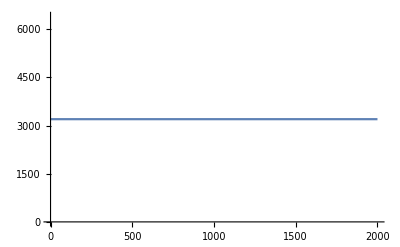
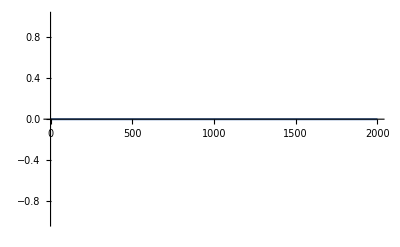
<|{2,1->2}→-Graphics-,{ex81,2->ex81}→-Graphics-,{1,en80->1}→-Graphics-,{1,1->2}→-Graphics-,{2,2->ex81}→-Graphics-,{en80,en80->1}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.

```mathematica
Parameters=Module[{g,W,V,H},g=If[beta==0,Log,Function[{m},m^beta]];
W=Function[{x,A},A Sin[2 Pi (x+1/4)]^2];
V=Function[{x},W[x,A]];
H=Function[{x,p,m},p^2/(2 m^alpha)+V[x]-g[m]];
Association[{"alpha"->alpha,"beta"->beta,"g[m]"->g,"W[x,A]"->W,"V[x]"->V,"H[x,p,m]"->H}]]
```

<|alpha→alpha,beta→beta,g[m]→If[beta==0,Log,Function[{m},m^beta]],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1255[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1255[x$]-g$1255[m$]]|>

```mathematica
alpha=1;beta=0;A=1;Parameters
```

<|alpha→alpha,beta→beta,g[m]→If[beta==0,Log,Function[{m},m^beta]],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1255[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1255[x$]-g$1255[m$]]|>

```mathematica
<<Examples/Parameters'
```

Get::noopen: Cannot open Examples/Parameters.

$Failed'

```mathematica
Needs["AWSLink`","/Users"]
```

```mathematica
FileNames[]
```

{.account,Applications,.bash_history,.bash_sessions,.CFUserTextEncoding,.config,Desktop,Documents,Downloads,.dropbox,Dropbox,.DS_Store,.eclipse,eclipse,eclipse-workspace,.gitconfig,Library,Movies,Music,.oracle_jre_usage,.p2,Pictures,Public,.tooling,.Trash,.viminfo,.vscode}

```mathematica
alpha=1;
beta=0;
A=1;
Needs["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
```

Needs::cxt: Invalid context specified at position 1 in Needs[/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m]. A context must consist of valid symbol names separated by and ending with `.

Needs[/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m]

```mathematica
Parameters["V[x]"][x]
```

Sin[2 π (1/4+x)]^2